```mathematica
ContractCount[g_]:=Block[{from= {VertexCount[g],EdgeCount[g]}},
Table[
With[{h=VertexContract[g,{nonedge[[1]],nonedge[[2]]}]},
from->{VertexCount[h],EdgeCount[h]}
],
{nonedge,EdgeList[GraphComplement[g]]}
]
]
```

```mathematica
PlanarLabels[vertices_]:=Map[#->If[#[[1]]*3-6==#[[2]],Framed[ToString[#]],ToString[#]]&,vertices
]
```

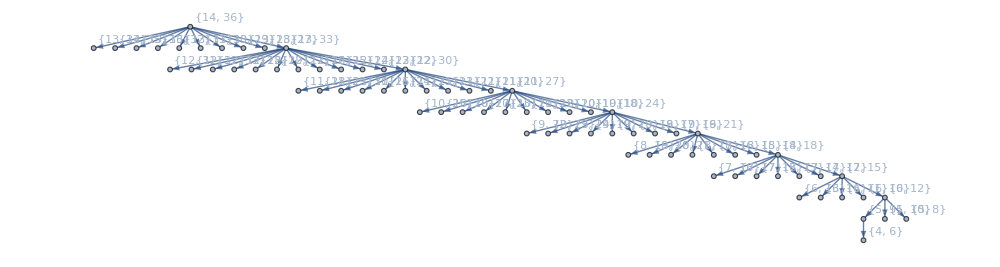

```mathematica
gg=With[
{g=Monitor[Graph[DeleteDuplicates[Flatten[Table[DeleteDuplicates[ContractCount[ReadGrof[k]]],{k,1,300000}]]]],k]},
Graph[EdgeList[g], VertexLabels->PlanarLabels[VertexList[g]], GraphLayout->"LayeredDigraphEmbedding", ImageSize->1000]
]
```

```mathematica
Table[VertexOutDegree[gg,k],{k,Sort[Select[VertexList[gg],VertexOutDegree[gg,#]>0&]]}]
```

{1,3,5,7,8,9,10,11,12,10}

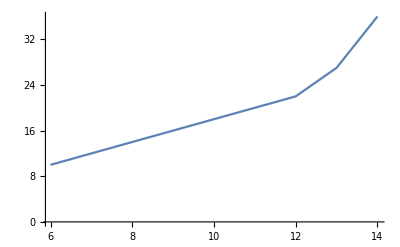

```mathematica
Table[{level,Map[Last,Select[VertexList[gg],#[[1]]==level&]]//Min},{level,6,14}]//ListLinePlot
```

```mathematica
ma=Table[{level,Map[Last,Select[VertexList[gg],#[[1]]==level&]]//Max},{level,6,14}]
```

{{6,14},{7,18},{8,21},{9,24},{10,27},{11,30},{12,33},{13,36},{14,36}}

```mathematica
mi=Table[{level,Map[Last,Select[VertexList[gg],#[[1]]==level&]]//Min},{level,6,14}]
```

{{6,10},{7,12},{8,14},{9,16},{10,18},{11,20},{12,22},{13,27},{14,36}}

```mathematica
Map[Last,ma-mi]
```

{4,6,7,8,9,10,11,9,0}